```mathematica
qubit0:={{1},{0}}
qubit1:={{0},{1}}
qubit:={qubit0,qubit1}
phys1:=KroneckerProduct[qubit0,qubit0,qubit0,qubit0]
phys2:=KroneckerProduct[qubit0,qubit1,qubit1,qubit1]
phys3:=KroneckerProduct[qubit1,qubit0,qubit1,qubit0]
phys4:=KroneckerProduct[qubit1,qubit1,qubit0,qubit1]
phys:={phys1,phys2,phys3,phys4}
SU2H[g_]:=1/g^2 {{0,-2,0,-2},{-2,3g^4,-1/2,0},{0,-1/2,3g^4,-1/2},{-2,0,-1/2,3g^4}}+500IdentityMatrix[4]
```

```mathematica
energyEigenvalue[g_,n_]:=Part[Eigenvalues[SU2H[g]],4-n]-500;
energyEigenstateCoefficient[g_,n_,a_]:=Part[Part[Eigenvectors[SU2H[g]],4-n],a];
dE[g_,n_]:=D[energyEigenvalue[g,n],g];
```

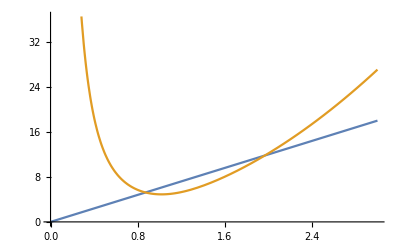

```mathematica
Plot[{Evaluate[dE[g,3]],energyEigenvalue[g,3]},{g,0,3Sqrt[0.999]}]
```

```mathematica
groundState[g_]:=Sum[energyEigenstateCoefficient[g,0,i]Part[phys,i],{i,1,4}]
densityMatrix[g_]:=groundState[g].Transpose[groundState[g]]
leftBasis:={KroneckerProduct[qubit0,qubit0,qubit0],KroneckerProduct[qubit0,qubit0,qubit1],KroneckerProduct[qubit0,qubit1,qubit0],KroneckerProduct[qubit1,qubit0,qubit0],KroneckerProduct[qubit0,qubit1,qubit1],KroneckerProduct[qubit1,qubit0,qubit1],KroneckerProduct[qubit1,qubit1,qubit0],KroneckerProduct[qubit1,qubit1,qubit1]}
RDM1[g_]:=Sum[Part[Transpose[KroneckerProduct[Part[qubit,k],Part[leftBasis,i]]].densityMatrix[g].KroneckerProduct[Part[qubit,k],Part[leftBasis,j]],1,1]Part[leftBasis,i].Transpose[Part[leftBasis,j]],{i,1,8},{j,1,8},{k,1,2}]
S[g_]:=-Part[Eigenvalues[RDM1[g]],1]Log[2,Part[Eigenvalues[RDM1[g]],1]]-Part[Eigenvalues[RDM1[g]],2]Log[2,Part[Eigenvalues[RDM1[g]],2]]
```

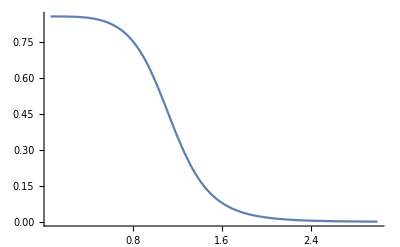

```mathematica
Plot[S[g],{g,0.06,3Sqrt[0.999]}]
```

```mathematica
EntropyData:=Table[{g,S[g]},{g,Range[0.06,3Sqrt[0.999],0.001]}]
FindFit[EntropyData, a Tanh[b g + c]+d,{{a,0.1},{b,-4},{c,3.6},{d,1}},g]
```

{a→0.428929,b→-2.70915,c→3.07854,d→0.435845}

```mathematica
EntropyFunction[g_]:=0.42892928712499195Tanh[-2.7091473871799394g+3.0785411207799562]+0.4358447191944868
```

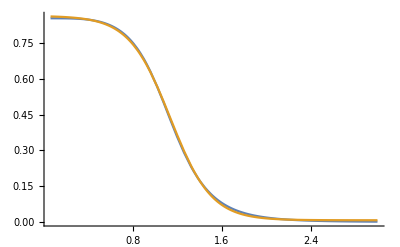

```mathematica
Plot[{S[g],EntropyFunction[g]},{g,0.06,3Sqrt[0.999]}]
```

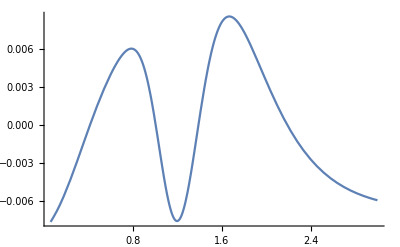

```mathematica
Plot[S[g]-EntropyFunction[g],{g,0.06,3Sqrt[0.999]}]
```

```mathematica
dEntropyFunction[g_]:=D[EntropyFunction[g],g]
```

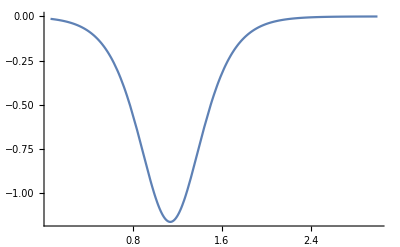

```mathematica
Plot[Evaluate[dEntropyFunction[g]],{g,0.06,3Sqrt[0.999]}]
```

```mathematica
β[g_]:=dEntropyFunction[g]/dE[g,3]
```

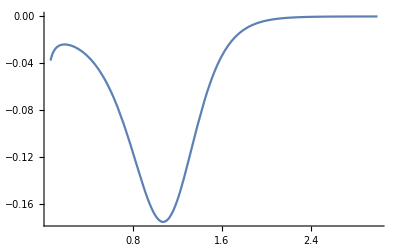

```mathematica
Plot[Evaluate[β[g]],{g,0.06,3Sqrt[0.999]}]
```

Negative temperatures suggests that the system should preferentially gather in higher energy states, but this is calculated specifically for the ground state. So how do you interpret a negative temperature? Essentially says that the entropy decreases as you pump more energy into it, which should indicate that the system wants to reduce the amount of energy it has. The dynamic variable is g, so the system should prefer lower coupling constants overall to increase the entanglement entropy, assuming that entanglement entropy is monotonically increasing. The thing is, I don’t think that’s true. If we consider A and B as entangled systems, we could have C interact with B to destroy the entanglement between A and B and creating entanglement between B and C; but there’s no reason that the amount of entanglement between B and C should be greater than that between A and B.